-Graphics-
Image source: Histomap, published by Rand McNally in 1931

# Computational History

Jozsef Konczer

@ Milestone Institute

## Questions:

What kind of Historical countries existed in Europe?

How are these connected to each other?

How can we quantify relatedness, or impact?

How are Historical Countries related to present Countries?

## Definitions:

We will use Entities to represent Countries and Historical Countries:

WolframAlphaQueryParseResults

Hungary

WolframAlphaQueryParseResults

United Kingdom

WolframAlphaQueryParseResults

Roman Empire

To capture relatedness we will extract “StartDat”, “EndDate”, and “Polygon” from these entities:

```mathematica
Entity["HistoricalCountry","RomanEmpire"]["Properties"]
```

{center coordinates,current countries,end date,entity classes,full name,has polygon?,name,nationality,polygon,position,start date}

```mathematica
Entity["HistoricalCountry","RomanEmpire"][{"StartDate","EndDate","Polygon"}]
```

{Wed 16 Jan -27,Year: 395,Polygon[GeoPosition[…]]}

We will rely on the Wolfram database, not trying to correct nuances, check resources, etc. (At least in the first round)

```mathematica
euCountries=EntityList[EntityClass["Country","Continent"->"Europe"]]
```

{Albania,Andorra,Austria,Belarus,Belgium,Bosnia and Herzegovina,Bulgaria,Croatia,Cyprus,Czech Republic,Denmark,Estonia,Faroe Islands,Finland,France,Germany,Gibraltar,Greece,Guernsey,Hungary,Iceland,Ireland,Isle of Man,Italy,Jersey,Kosovo,Latvia,Liechtenstein,Lithuania,Luxembourg,North Macedonia,Malta,Moldova,Monaco,Montenegro,Netherlands,Norway,Poland,Portugal,Romania,San Marino,Serbia,Slovakia,Slovenia,Spain,Svalbard,Sweden,Switzerland,Ukraine,United Kingdom,Vatican City}

Even this is can change depending on the source:
Wikipedia, The World Factbook, Our World in Data

```mathematica
euCountries//Length
```

51

```mathematica
GeoGraphics[Polygon/@euCountries]
```

-Graphics-

## Abstraction:

```mathematica
Entity["HistoricalCountry","Czechoslovakia"][{"StartDate","EndDate","Polygon"}]
```

{Mon 28 Oct 1918,Thu 31 Dec 1992,Polygon[GeoPosition[…]]}

```mathematica
{QuantityMagnitude[DateDifference[DateObject[{2000}],DateObject[{1918,10,28},"Day"],"Days"]],QuantityMagnitude[DateDifference[DateObject[{2000}],DateObject[{1992,12,31},"Day"],"Days"]],Polygon[GeoPosition[…]][[1,1]]//Short}
```

{-29650,-2557,{{{51.0096,14.5415},{50.9944,14.5701},«472»,{51.0096,14.5415}}}}

```mathematica
(*From https://mathematica.stackexchange.com/questions/18196/thick-polygons-in-graphics3d*)
raisePolygonEdge[p_Polygon,h_:1]:=Module[{data=p[[1]],pts},If[Depth[data]==3,data={data}];
pts=Flatten[Partition[Riffle[Most@#,Rest@#],2]&/@data,1];
Polygon[Join[{{#[[1,1]],#[[1,2]],0},{#[[1,1]],#[[1,2]],h},{#[[2,1]],#[[2,2]],h},{#[[2,1]],#[[2,2]],0}}&/@pts,data/. {a_?NumericQ,b_?NumericQ}:>{a,b,h}]]]
```

```mathematica
Graphics3D[raisePolygonEdge[Polygon[{#[[1]],#[[2]],1}&/@First[Polygon[GeoPosition[…]][[1,1]]]],1]]
```

-Graphics3D-

Connectedness of these Space-Time Countries, possibly including their Shadows.

## Computation:

```mathematica
Monitor[euExitingHistoricalCountries0=Table[Entity["HistoricalCountry",euCountries[[k]]["Name"]],{k,1,Length[euCountries]}],{k,Length[euCountries]}]
```

{Albania,Andorra,Austria,Belarus,Belgium,Entity[HistoricalCountry,Bosnia and Herzegovina],Bulgaria,Croatia,Cyprus,Entity[HistoricalCountry,Czech Republic],Denmark,Estonia,Entity[HistoricalCountry,Faroe Islands],Finland,France,Germany,Gibraltar,Greece,Guernsey,Hungary,Iceland,Ireland,Entity[HistoricalCountry,Isle of Man],Italy,Jersey,Kosovo,Latvia,Liechtenstein,Lithuania,Luxembourg,Entity[HistoricalCountry,North Macedonia],Malta,Moldova,Monaco,Montenegro,Netherlands,Norway,Poland,Portugal,Romania,Entity[HistoricalCountry,San Marino],Serbia,Slovakia,Slovenia,Spain,Svalbard,Sweden,Switzerland,Ukraine,Entity[HistoricalCountry,United Kingdom],Entity[HistoricalCountry,Vatican City]}

```mathematica
euExitingHistoricalCountries=Select[euExitingHistoricalCountries0,Not[MatchQ[#["StartDate"],Missing[__]]]&]
```

{Albania,Andorra,Austria,Belarus,Belgium,Bulgaria,Croatia,Cyprus,Denmark,Estonia,Finland,France,Germany,Greece,Hungary,Iceland,Ireland,Italy,Kosovo,Latvia,Liechtenstein,Lithuania,Luxembourg,Malta,Moldova,Monaco,Montenegro,Netherlands,Norway,Poland,Portugal,Romania,Serbia,Slovakia,Slovenia,Spain,Sweden,Switzerland,Ukraine}

```mathematica
Monitor[
euHistoricalCountries=Table[EntityList[EntityClass["HistoricalCountry","CurrentCountries"->euCountries[[k]]]],{k,1,Length[euCountries]}],
{k,Length[euCountries]}]//Short
```

{{Albania,Ancient Epirus,Austria-Hungary,Autonomous Albanian Republic of Korçë,Byzantine Empire,County of Sicily,Despotate of Arta,Empire of Nicaea,Bulgarian Empire,Illyria,Kingdom of Albania,Macedonia (ancient kingdom),Kingdom Of Serbia Medieval,Latin Empire,League of Lezhë,Molossians,Nazi Germany,Odrysian kingdom,Ostragothic Kingdom,Ottoman Empire,Post Serbian Empire States,Princedom of Albania,Principality of Albania,Principality of Kastrioti,Principality of Gjirokastër,Roman Empire,Roman Republic,Bulgarian Empire,Kingdom of Italy,Seleucid Empire,Serbian Empire,Serbian Grand Principality,Socialist People's Republic of Albania,Western Roman Empire},{Abbasid Caliphate,Andorra,Austrasia,Emirate Cordoba,First French Empire,Gallic Empire,Aragon,Kingdom of France,Kingdom Franks,Kingdom of Spain,Kingdom of the Visigoths,Neustria,Orléans,Paris,Roman Empire,Roman Republic,Umayyad Caliphate,Western Roman Empire,West Francia},«47»,{Alt Clud,Bell Beaker culture,Bernicia,Commonwealth of England, Scotland and Ireland,Brycheiniog,Bryneich,Calchfynedd,Ceredigion,Chichen Itza,Circinn,Dál Riata,Danelaw,Deheubarth,Deira,Dogfeiling,Dumnonia,Dumnonia,Dunoting,Dyfed,East Anglia,Ebrauc,Elmet,Essex,Fidach,Fortriu,Fotla,Gaini,Gallic Empire,Gododdin,Gwent,Gwerthyrnion,Kingdom of Gwynedd,Haestingas,Hicca,Hwicce,Kent,Cait,Ce,Kingdom of England,Fib,United Kingdom of Great Britain and Ireland,Kingdom of Ireland,Kingdom of Lindsey,Kingdom of Scotland,Lordship of Ireland,Magonsæte,Maelienydd,Mayapan,Medieval Kingdom Of Denmark,Medieval Kingdom Of Norway,Meirionnydd,Mercia,Middle Saxons,Morgannwg,Northumbria,Pecsætna,Pengwern,Powys,Principality of Wales,Rheged,Rhos,Rhufoniog,Roman Empire,Seisyllwg,Sussex,Suthrege,Uí Liatháin,United Kingdom,United Kingdom of Great Britain,Valentia,Welsh Kingdoms,Kingdom of Wessex,Western Roman Empire,Witware,Wreocensæte},{Byzantine Empire,First French Empire,Kingdom Lombards,Nazi Germany,Ostragothic Kingdom,Papal States,Repubblica Romana,Roman Empire,Roman Kingdom,Roman Republic,Kingdom of Italy,United Kingdom,Vatican City,Western Roman Empire}}

```mathematica
Shallow[euHistoricalCountriesUnion=Union[Flatten[euHistoricalCountries]]]
```

{Abbasid Caliphate,Achaean League,Aetolian League,Aidhne,Aileach,Airgíalla,Akragas,Albania,Albarracín,Alemanni,«657»}

```mathematica
Monitor[
euFilteredHistoricalCountriesUnion=Table[If[euHistoricalCountriesUnion[[k]]["HasPolygon"],euHistoricalCountriesUnion[[k]],Nothing[]],{k,1,Length[euHistoricalCountriesUnion]}],
{k,Length[euHistoricalCountriesUnion]}]//Shallow
```

{Abbasid Caliphate,Achaean League,Aetolian League,Albania,Albarracín,Alemanni,Algarve,Almería,Almohad Dynasty,Almoravid Dynasty,«345»}

```mathematica
Monitor[
euNamePolygonDates=Table[{euFilteredHistoricalCountriesUnion[[k]]["FullName"],euFilteredHistoricalCountriesUnion[[k]]["Polygon"],euFilteredHistoricalCountriesUnion[[k]]["StartDate"],euFilteredHistoricalCountriesUnion[[k]]["EndDate"]},{k,1,Length[euFilteredHistoricalCountriesUnion]}],
{k,Length[euFilteredHistoricalCountriesUnion]}]//Short
```

{{Abbasid Caliphate,Polygon[GeoPosition[…]],Year: 750,Wed 20 Feb 1258},«353»,{Taifa of Zaragoza,Polygon[GeoPosition[…]],Year: 1018,Year: 1118}}

```mathematica
Short[euNamePolygonDatesDeleteMissing=Table[If[MissingQ[hc[[3]]]||MissingQ[hc[[4]]],Nothing[],hc],{hc,euNamePolygonDates}]]
```

{{Abbasid Caliphate,Polygon[GeoPosition[…]],Year: 750,Wed 20 Feb 1258},«308»,{Taifa of Zaragoza,Polygon[GeoPosition[…]],Year: 1018,Year: 1118}}

```mathematica
Short[euSortedNamePolygonDates=SortBy[euNamePolygonDatesDeleteMissing,QuantityMagnitude[DateDifference[#[[4]],DateObject[{2000}]]]&]]
```

{{State Union of Serbia and Montenegro,Polygon[GeoPosition[…]],Tue 4 Feb 2003,Mon 5 Jun 2006},«308»,{Cycladic civilization,Polygon[«1»],«1»,Year: -2000}}

#### Examine the Data

```mathematica
euSortedNamePolygonDates[[;;10,2]]
```

{Polygon[GeoPosition[…]],Polygon[GeoPosition[…]],Polygon[GeoPosition[…]],Polygon[GeoPosition[…]],Polygon[GeoPosition[…]],Polygon[GeoPosition[…]],Polygon[GeoPosition[…]],Polygon[GeoPosition[…]],Polygon[GeoPosition[…]],FilledCurve[{{Line[GeoPosition[…]]},{Line[GeoPosition[…]]},{Line[GeoPosition[…]]},{Line[GeoPosition[…]]},{Line[GeoPosition[…]]},{Line[GeoPosition[…]]},{Line[GeoPosition[…]]},{Line[GeoPosition[…]]}}]}

```mathematica
euSortedNamePolygonDates[[1,2]]
```

Polygon[GeoPosition[…]]

```mathematica
euSortedNamePolygonDates[[1,2]][[1,1]]//Short
```

{{{46.1494,19.9841},{46.1509,20.1357},«382»,{46.1494,19.9841}}}

```mathematica
euSortedNamePolygonDates[[5,2]]
```

Polygon[GeoPosition[…]]

```mathematica
euSortedNamePolygonDates[[5,2]][[1,1]]//Shallow
```

{{{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},«443»},{{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},«13»},{{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},«11»},{{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},«1»}}

```mathematica
euSortedNamePolygonDates[[10,2]]
```

FilledCurve[{{Line[GeoPosition[…]]},{Line[GeoPosition[…]]},{Line[GeoPosition[…]]},{Line[GeoPosition[…]]},{Line[GeoPosition[…]]},{Line[GeoPosition[…]]},{Line[GeoPosition[…]]},{Line[GeoPosition[…]]}}]

```mathematica
euSortedNamePolygonDates[[10,2]][[1,;;,1,1,1]]//Shallow
```

{{{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},«317»},{{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},«51»},{{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},«23»},{{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},«15»},{{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},«3»},{{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},«7»},{{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»}},{{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»}}}

```mathematica
Tally[Head/@euSortedNamePolygonDates[[;;,2]]]
```

{{Polygon,305},{FilledCurve,5}}

#### Export to JSON

```mathematica
Monitor[
euHistoricalStatesJSON=Association@@Table[
TextString[euSortedNamePolygonDates[[k]][[1]]]->
Association@@{
"start"->TextString[euSortedNamePolygonDates[[k]][[3]],DateFormat->{"Year","-","Month","-","Day"}],
"end"->TextString[euSortedNamePolygonDates[[k]][[4]],DateFormat->{"Year","-","Month","-","Day"}],
"territory_geolocations"->Switch[
Head[euSortedNamePolygonDates[[k]][[2]]],
Polygon,euSortedNamePolygonDates[[k]][[2]][[1,1]],
FilledCurve,euSortedNamePolygonDates[[k]][[2]][[1,;;,1,1,1]]
]
}
,{k,1,Length[euSortedNamePolygonDates]}]
,{k,Length[euSortedNamePolygonDates]}
];
```

```mathematica
Export[NotebookDirectory[]<>"/EuHistoricalStates.json",euHistoricalStatesJSON,"RawJSON"]
```

```mathematica
Short[data=Import[NotebookDirectory[]<>"/EuHistoricalStates.json","RawJSON"]]
```

<|State Union of Serbia and Montenegro→<|start→2003-02-04,«1»,territory_geolocations→{{{46.1494,19.9841},«383»,{«19»,«16»}}}|>,«302»|>

```mathematica
data//Dataset
```

Dataset[<>]

#### Defining temporal relatedness

```mathematica
canEffect[npd1_,npd2_]:=
(*The first Does not Start later then the End of the second*)
Not[QuantityMagnitude[DateDifference[DateObject[{0}],npd1[[3]],"Days"]]>QuantityMagnitude[DateDifference[DateObject[{0}],npd2[[4]],"Days"]]]&&
(*There is an Overlap between the Shadows of the states (A shadow is extended by 100 years after the End)*)
RegionMeasure[IntervalIntersection[
(*First Shadow*)Interval[{QuantityMagnitude[DateDifference[DateObject[{0}],npd1[[3]],"Days"]],QuantityMagnitude[DateDifference[DateObject[{0}],npd1[[4]],"Days"]]+365 100}],
(*Second Shadow*)Interval[{QuantityMagnitude[DateDifference[DateObject[{0}],npd2[[3]],"Days"]],QuantityMagnitude[DateDifference[DateObject[{0}],npd2[[4]],"Days"]]+365 100}]]
]>0
```

```mathematica
Monitor[
caneffectArray=Table[
canEffect[euSortedNamePolygonDates[[jj]],euSortedNamePolygonDates[[ii]]]//Boole

,{jj,1,Length[euSortedNamePolygonDates]},{ii,1,Length[euSortedNamePolygonDates]}]
,{ii,jj}]//ArrayPlot

Export[NotebookDirectory[]<>"/CanEffectArray.txt",caneffectArray]
```

-Graphics-

```mathematica
caneffectArray=ToExpression[Import[NotebookDirectory[]<>"/CanEffectArray.txt","List"]];
```

```mathematica
TimelinePlot[DateInterval[{#[[3]],#[[4]]}]&/@euSortedNamePolygonDates]
```

-Graphics-

#### Regions

```mathematica
ToRegion2[npd1_]:=Module[
{geoRegion},
geoRegion=npd1[[2]];
If[Head[geoRegion]==Polygon,
If[npd1[[1]]=="French Fourth Republic",
Return[MeshRegion[Polygon[#[[1;;-1;;2]]]]&/@(geoRegion[[1,1]])],
Return[MeshRegion[Polygon[#[[1;;-1;;4]]]]&/@(geoRegion[[1,1]])];
]
];
If[Head[geoRegion]==FilledCurve,
Return[Flatten[{(geoRegion/.{GeoPosition[p_]:>p,Line->Polygon}/.Polygon[x_]:>MeshRegion[Polygon[x]]/.FilledCurve[x_]:>{x})}]];
];
]
```

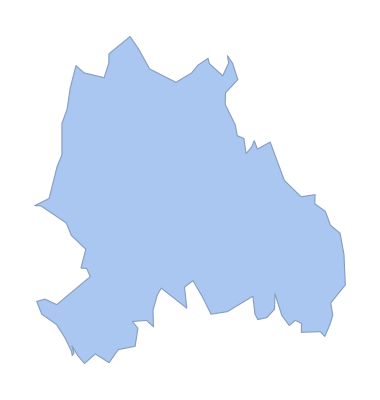
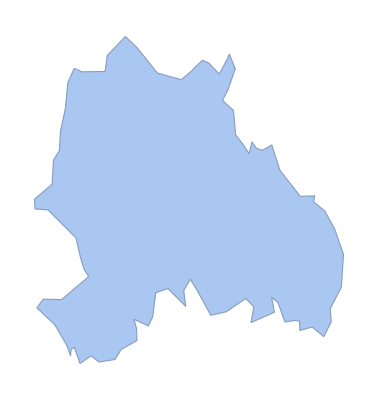
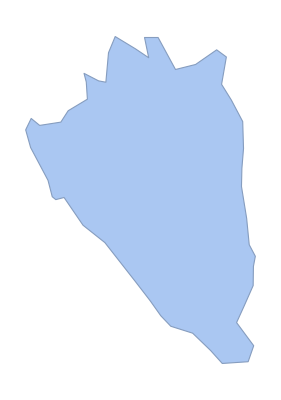
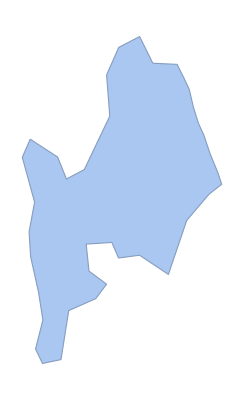
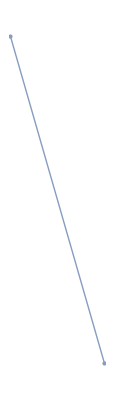
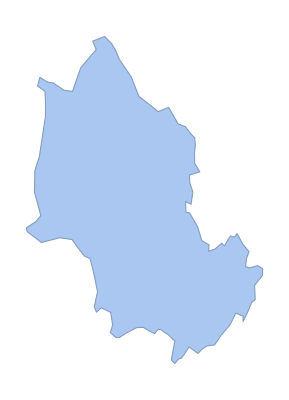
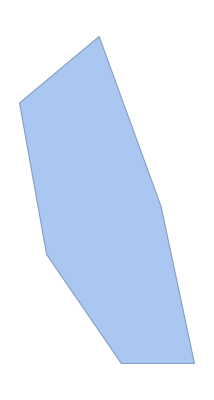
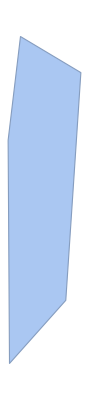

```mathematica
Table[ToRegion2[euSortedNamePolygonDates[[k]]],{k,1,5}]
```

```mathematica
RL0=ToRegion2/@(euSortedNamePolygonDates[[;;]]);
```

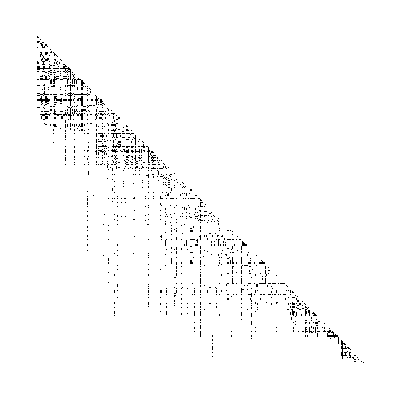

```mathematica
Monitor[
(overlapArray=Table[
If[caneffectArray[[k,l]]==1||caneffectArray[[l,k]]==1,
Not[And@@Flatten[Table[RegionDisjoint[R1,R2],{R1,#[[1]]},{R2,#[[2]]}]]]&[{RL0[[k]],RL0[[l]]}],
False
],
{k,2,Length[RL0]},{l,1,k-1}]//Boole)//ArrayPlot,
{k,l}]
```

```mathematica
overlapArray
```

overlapArray

```mathematica
Export[NotebookDirectory[]<>"/OverlapArray.txt",overlapArray]
```

```mathematica
overlapArray==ToExpression[Import[NotebookDirectory[]<>"/OverlapArray.txt","List"]]
```

overlapArray=={{1},307,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,30,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}
 |  |  |  |

```mathematica
overlapArray=ToExpression[Import[NotebookDirectory[]<>"/OverlapArray.txt","List"]]
```

{{1},307,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}
 |  |  |  |

```mathematica
(causalArray=Table[caneffectArray[[ii,jj]]If[ii==jj,0,If[ii>jj,overlapArray[[ii-1,jj]],overlapArray[[jj-1,ii]]]],{ii,1,Length[euSortedNamePolygonDates]},{jj,1,Length[euSortedNamePolygonDates]}])//ArrayPlot
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"/CausalArray.txt",causalArray]
```

```mathematica
causalArray==ToExpression[Import[NotebookDirectory[]<>"/CausalArray.txt","List"]]
```

True

```mathematica
Export[NotebookDirectory[]<>"AdjacencyMatrix.txt",causalArray]
```

#### Graph representation

```mathematica
euHistoryAdjacencyMatrix=ToExpression[Import[NotebookDirectory[]<>"AdjacencyMatrix.txt","List"]]
```

{1}
 |  |  |  |

```mathematica
euHistoryGraph=AdjacencyGraph[euHistoryAdjacencyMatrix[[;;,;;]]];
```

```mathematica
GraphPlot[euHistoryGraph]
```

-Graphics-

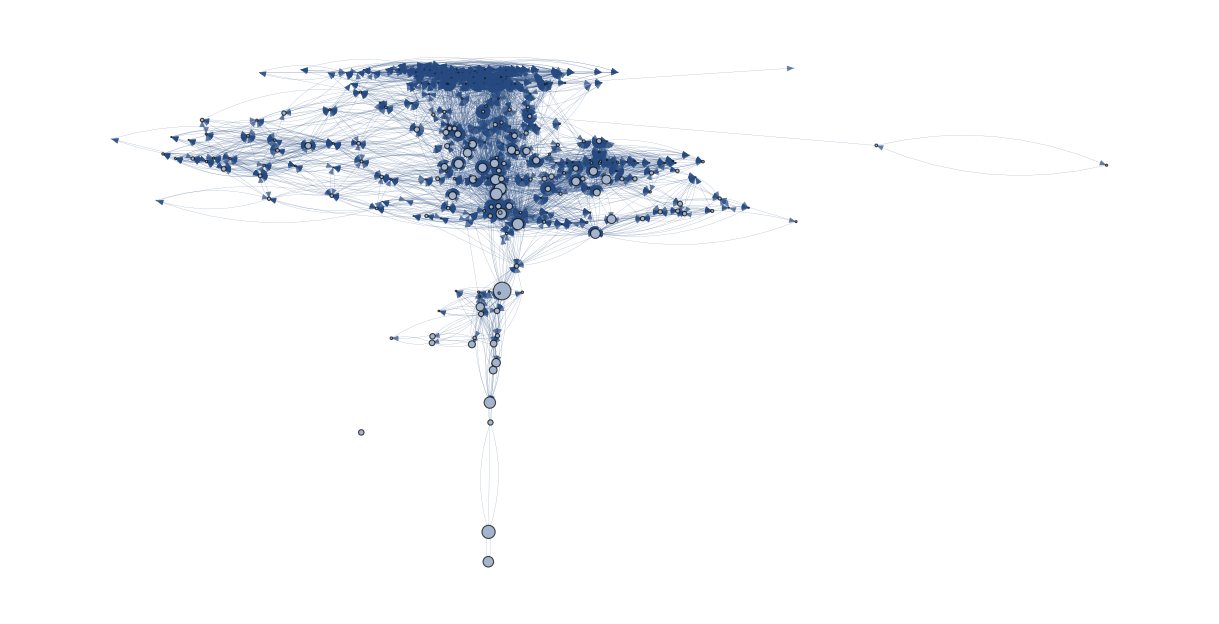

```mathematica
With[{nn=310},
Graph[
euHistoryGraph,

EdgeStyle->Thickness[0.0001],
EdgeShapeFunction->GraphElementData[{"Arrow","ArrowSize"->0.001}],
VertexLabels->
Thread[Range[Length[euSortedNamePolygonDates[[;;nn]]]]->(Placed[#[[1]],Tooltip]&/@euSortedNamePolygonDates[[;;nn]])],
VertexCoordinates->
Thread[Range[nn]->Table[{Automatic,QuantityMagnitude[DateDifference[DateObject[{0}],euSortedNamePolygonDates[[k]][[3]],"Days"]]},{k,1,nn}]],
VertexSize->
Thread[Range[nn]->Table[-0.00005QuantityMagnitude[DateDifference[euSortedNamePolygonDates[[k]][[4]],euSortedNamePolygonDates[[k]][[3]],"Days"]],{k,1,nn}]]
,AspectRatio->1/2,ImageSize->1000]
]
```

## Interpretation:

We were able to show European Historical countries from another perspective

However:

The data is controversial

During cleaning we filtered out a big portion of States

```mathematica
Length[euHistoricalCountriesUnion]
Length[euSortedNamePolygonDates]
```

667

310

The causation relation was arbitrary (100 year old shadow overlap)

The Polygon of a Historical Country was fixed, no changes in area were addressed

The data sets may have an USA/EU centric bias

## Questions II

How to Improve the data?

How to perform the calculations more effectively?

How to check and validate the results?

How to do more insightful visualizations?

## Further Resources

Spatial and Temporal visualization:

https://nodegoat.net/

The Programming Historian

https://programminghistorian.org/

Optical character recognition

https://readcoop.eu/transkribus/

https://reference.wolfram.com/language/ref/TextRecognize.html